```mathematica
(*(.10Mathematica)*)
```

```mathematica
w={2,-1+y*I,-1-y*I}
```

{2,-1+ⅈ y,-1-ⅈ y}

```mathematica
(*special Weierstrass cubic polynomial*)
```

```mathematica
ExpandAll[Product[x-w[[i]],{i,3}]]
```

-2-3 x+x^3-2 y^2+x y^2

```mathematica
Clear[p]
```

```mathematica
p[x_]=-2-3 x+x^3-2 y^2+x y^2
```

-2-3 x+x^3-2 y^2+x y^2

```mathematica
CoefficientList[ExpandAll[Product[x-w[[i]],{i,3}]],x]
```

{-2-2 y^2,-3+y^2,0,1}

```mathematica
D[{-2-2 y^2,-3+y^2},{y,1}]
```

{-4 y,2 y}

```mathematica
CoefficientList[ExpandAll[Product[x-w[[i]],{i,3}]],y]
```

{-2-3 x+x^3,0,-2+x}

```mathematica
Solve[2-3 x+x^3==0,x]
```

{{x→-2},{x→1},{x→1}}

```mathematica
p[x]/.y->1
```

(-ⅈ)[x]

```mathematica
4*(-4-2 x+x^3)
```

4 (-4-2 x+x^3)

```mathematica
p[x]/.y->0
```

(-ⅈ)[x]

```mathematica
4*(-2-3 x+x^3)
```

4 (-2-3 x+x^3)

```mathematica
p[x]/.y->Sqrt[3]
```

(-ⅈ)[x]

```mathematica
v=CoefficientList[4*p[x],x]
```

{4 (-ⅈ)[x]}

```mathematica
g2=-v[[2]]
```

Part::partw: Part 2 of {4 (-ⅈ)[x]} does not exist.

-{4 (-ⅈ)[x]}⟦2⟧

```mathematica
g3=-v[[1]]
```

-4 (-ⅈ)[x]

```mathematica
(*the j invariant*)
```

```mathematica
j=FullSimplify[g2^3/(g2^3-27*g2^2)]
```

1-27/(27+{4 (-ⅈ)[x]}⟦2⟧)

```mathematica
N[1-27/(15+4 y^2)/.y->{0,1,2,Sqrt[3],1/Sqrt[2],1/Sqrt[3],1/2,1/3,1/4,1/5}]
```

{-0.8,-0.421053,0.129032,0.,-0.588235,-0.653061,-0.6875,-0.748201,-0.770492,-0.781003}

```mathematica
NSolve[15+4 y^2==27,y]
```

{{y→-1.73205},{y→1.73205}}

```mathematica
NSolve[15+4 y^2==-27,y]
```

{{y→0.-3.24037 ⅈ},{y→0.+3.24037 ⅈ}}

```mathematica
(*plot the the j invariant*)
```

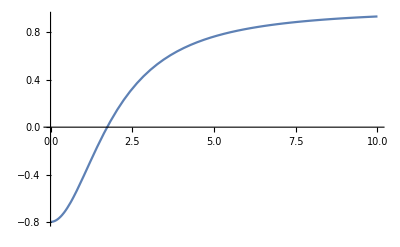

```mathematica
Plot[1-27/(15+4 y^2),{y,0,10}]
```

```mathematica
(*special case traces*)
```

```mathematica
N[FullSimplify[1+I*Sqrt[3]+1/(1+I*Sqrt[3])]]
```

1.25+1.29904 ⅈ

```mathematica
N[FullSimplify[1+I/Sqrt[3]+1/(1+I/Sqrt[3])]]
```

1.75+0.144338 ⅈ

```mathematica
N[FullSimplify[1+I/2+1/(1+I/2)]]
```

1.8+0.1 ⅈ

```mathematica
(*close to the Nylander butterfly trace*)
```

```mathematica
N[FullSimplify[1+I/3+1/(1+I/3)]]
```

1.9+0.0333333 ⅈ

```mathematica
N[FullSimplify[1+I/4+1/(1+I/4)]]
```

1.94118+0.0147059 ⅈ

```mathematica
N[FullSimplify[1+I/5+1/(1+I/5)]]
```

1.96154+0.00769231 ⅈ

```mathematica
(*end*)
```

```mathematica
(* mathematica *)
Clear[cr,cols,cr2,cr3,cr4,firstCols,s,s0]
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
cr3[n_]:=cr3[n]=cols[[n+8]];
cr4[n_]:=cr4[n]=cols[[n+12]];
cr5[n_]:=cr5[n]=cols[[n+16]]
Clear[mu,a,b,A,B,x,y,t,n]
(* the Möbius transforms : Kleiniamn group in SL(2,c) :Granny approach*)
```

```mathematica
(*1. two-trace parameters and Granny matrices*)
ta=1.9+0.03333333333333333 ⅈ
tb=1.9-0.03333333333333333 ⅈ
tab=0.5(ta tb-Sqrt[ta^2tb^2-4(ta^2+tb^2)]);z0=(tab-2)tb/(tb tab-2ta+2I tab);
a={{ta/2,(ta tab-2tb+4I)/(2tab+4)/z0},{(ta tab-2 tb-4I)z0/(2tab-4),ta/2}};A=Inverse[a];b=0.5{{tb-2I,tb},{tb,tb+2I}};B=Inverse[b];
```

1.9+0.0333333 ⅈ

1.9-0.0333333 ⅈ

```mathematica
s[1]=a
s[2]=b
s[3]=A
s[4]=B
```

{{0.95+0.0166667 ⅈ,-0.0167132-0.0473504 ⅈ},{0.0534407-2.04612 ⅈ,0.95+0.0166667 ⅈ}}

{{0.95-1.01667 ⅈ,0.95-0.0166667 ⅈ},{0.95-0.0166667 ⅈ,0.95+0.983333 ⅈ}}

{{0.95+0.0166667 ⅈ,0.0167132+0.0473504 ⅈ},{-0.0534407+2.04612 ⅈ,0.95+0.0166667 ⅈ}}

{{0.95+0.983333 ⅈ,-0.95+0.0166667 ⅈ},{-0.95+0.0166667 ⅈ,0.95-1.01667 ⅈ}}

```mathematica
Affine[{z1_,z2_}]:=0.000001 Round[(z1/z2)/0.000001];
Children[{z_,n_}]:={Affine[{a,b,A,B}[[#]].{z,1}],#}&/@Delete[Range[4],{3,4,1,2}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,A,B}[[i]].{0,1}],i},{i,1,4}],12];
ll=Length[aa1]
```

2123224

```mathematica
Last[aa1]
aa=Delete[Union[aa1],Length[Union[aa1]]];
```

{2.68996,2.68385}

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-8,8},{-8,8}}/4,ColorFunction->Hue,Axes->False];
```

```mathematica
dlst=Table[1+Mod[Floor[1+(1+Floor[24*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

2

95

```mathematica
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->{{-8,8},{-8,8}}/4,Axes->False];
Export["Nylander_2group_granny_2trace_special_case_3rd_limitset_12_fractal_fields_g0g2.jpg",{g0,g2}]

(*end*)
```

Nylander_2group_granny_2trace_special_case_3rd_limitset_12_fractal_fields_g0g2.jpg

```mathematica
(*Fractal Field conformal map: Dot cross-.{1,0}*)
```

```mathematica
bb0=Delete[Reverse[Union[ParallelTable[{aa⟦i,1⟧/(aa⟦i,1⟧^2+aa⟦i,2⟧^2),aa⟦i,2⟧/(aa⟦i,1⟧^2+aa⟦i,2⟧^2)},{i,Length[aa]}]]],1];
```

```mathematica
ptlst1a=Point[Developer`ToPackedArray[bb0],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
ga=Graphics[{PointSize[.001],ptlst1a},AspectRatio->Automatic,ImageSize->2000,PlotRange->4*{{-1,1},{-1,1}},Background->Black];
```

```mathematica
Export["Nylander_2group_granny_2trace_special_case_3rd_limitset_11_fractal_field_ga.jpg",ga]
```

Nylander_2group_granny_2trace_special_case_3rd_limitset_11_fractal_field_ga.jpg

```mathematica
(*Fractal Field conformal map: Dot cross->{0,1}*)
```

```mathematica
Clear[bb]
bb=Delete[Reverse[Union[ParallelTable[{-aa⟦i,2⟧/(aa⟦i,1⟧^2+aa⟦i,2⟧^2),aa⟦i,1⟧/(aa⟦i,1⟧^2+aa⟦i,2⟧^2)},{i,Length[aa]}]]],1];
```

```mathematica
ptlst1a=Point[Developer`ToPackedArray[bb],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
gb=Graphics[{PointSize[.001],ptlst1a},AspectRatio->Automatic,ImageSize->2000,PlotRange->8*{{-1,1},{-1,1}},Background->Black];
```

```mathematica
gout=Show[{ga,gb,g0},PlotRange->4*{{-1,1},{-1,1}}];
```

```mathematica
Export["Nylander_2group_granny_2trace_special_case_3rd_limitset_11_fractal_fields_gout.jpg",gout]
```

Nylander_2group_granny_2trace_special_case_3rd_limitset_11_fractal_fields_gout.jpg

```mathematica
(*end*)
```

## (*Mathematica*) (*https://www.dhushara.com/DarkHeart/quasif/toolbox.htm*) (* ::Section::*)(*Core Möbius tools*)Clear[mobius,fixPoint]; mobius[T_,z_]:=(T[[1,1]] z+T[[1,2]])/(T[[2,1]] z+T[[2,2]]); fixPoint[T_]:=Module[{a,b,c,d,tr,tr2,k},{a,b,c,d}=Flatten[T]; tr=a+d; tr2=Tr[T.T]; k=((tr+Sqrt[tr2-4])/2)^2; If[Abs[k]>1,Sqrt[-(d-a)+Sqrt[(d-a)^2+4 b c]]/(2 c),Sqrt[-(d-a)-Sqrt[(d-a)^2+4 b c]]/(2 c)]]; (* ::Section::*) (*Grandma generators*) Clear[grandma]; grandma[ta_,tb_,posroot_:False,opt_:0,tab_:None]:=Module[{p,q,tabVal,z0,ab,a,b},p=-ta tb; q=ta^2+tb^2; tabVal=If[posroot,(-p+Sqrt[p^2-4 q])/2,(-p-Sqrt[p^2-4 q])/2]; z0=((tabVal-2) tb)/(tb tabVal-2 ta+2 I tabVal); ab={{tabVal/2,(tabVal-2)/(2 z0)},{(tabVal+2) z0/2,tabVal/2}}; b={{(tb-2 I)/2,tb/2},{tb/2,(tb+2 I)/2}}; a=ab.Inverse[b]; {a,b}]; (* ::Section::*)(*Plot buffer and helpers*)Clear[initBuffer,plotSegment]; initBuffer[size_]:=ConstantArray[256,{size,size}]; safeSetPixel[M_,r_,c_,co_]:=Module[{},If[IntegerQ[r]&&IntegerQ[c]&&1<=r<=Length[M]&&1<=c<=Length[M[[1]]],M[[r,c]]=co]; M]; plotSegment[M_,o_,n_,scale_,size_,color_]:=Module[{steps,zs,s2=size/2},steps=Max[2,Ceiling[Abs[scale (n-o)] size]]; zs=Table[o+(n-o) t,{t,0,1,1/(steps-1)}]; Do[If[NumericQ[z]&&z==z&&(*not NaN*)Max[Abs[Re[z]],Abs[Im[z]]]<1,M=safeSetPixel[M,Round[s2-s2*Re[z]],Round[s2-s2*Im[z]],color];],{z,zs}]; M]; FiniteQ[x_]:=NumericQ[x]&&x==x&&x!=ComplexInfinity; (* ::Section::*) (*Depth-first Kleinian renderer*) Clear[DepthFirstSegments]; DepthFirstSegments[A_,B_,ep_:0.001,levmax_:1000,spec_:0]:=Module[{epScaled=ep,posroot,a,b,gens,fix,word,tags,lev,maxLev,newpoint,oldpoint,midpoint,plt,segments},posroot=If[Mod[spec,8]>=4,True,False]; {a,b}=grandma[A,B,posroot,0]; gens={a,b,Inverse[a],Inverse[b]}; maxLev=If[levmax==0,10000,levmax]; fix=Table[0,{3},{4}]; Do[fix[[1,i]]=fixPoint[gens[[Mod[i-1,4,1]]].gens[[Mod[i-2,4,1]]].gens[[Mod[i-3,4,1]]].gens[[Mod[i-4,4,1]]]]; fix[[2,i]]=fixPoint[gens[[i]]]; fix[[3,i]]=fixPoint[gens[[Mod[i+1,4,1]]].gens[[Mod[i+2,4,1]]].gens[[Mod[i+3,4,1]]].gens[[Mod[i+4,4,1]]]];,{i,1,4}]; word=ConstantArray[IdentityMatrix[2],maxLev]; tags=ConstantArray[1,maxLev]; lev=1; tags[[1]]=1; word[[1]]=gens[[1]]; segments={}; While[!(lev==0&&tags[[1]]==2),plt=False; Which[MemberQ[{1},spec],newpoint=mobius[word[[lev]],fix[[1,tags[[lev]]]]]; oldpoint=mobius[word[[lev]],fix[[3,tags[[lev]]]]]; midpoint=mobius[word[[lev]],fix[[2,tags[[lev]]]]]; If[lev==maxLev||(Abs[newpoint-midpoint]<epScaled&&Abs[oldpoint-midpoint]<epScaled),plt=True],MemberQ[{0},spec],newpoint=mobius[word[[lev]],fix[[1,tags[[lev]]]]]; oldpoint=mobius[word[[lev]],fix[[3,tags[[lev]]]]]; If[lev==maxLev||Abs[newpoint-oldpoint]<epScaled,plt=True]]; If[plt,If[NumericQ[newpoint]&&NumericQ[oldpoint]&&newpoint==newpoint&&oldpoint==oldpoint,AppendTo[segments,{oldpoint,newpoint}]]; lev--; While[lev>0&&tags[[lev+1]]-1==Mod[tags[[lev]]+2,4],lev--]; If[lev==0&&tags[[1]]==2,Break[]]; lev++; tags[[lev]]=Mod[tags[[lev]]-1,4,1]; If[lev==1,word[[1]]=gens[[tags[[1]]]],word[[lev]]=word[[lev-1]].gens[[tags[[lev]]]]];,lev++; If[lev>maxLev,lev--; While[lev>0&&tags[[lev+1]]-1==Mod[tags[[lev]]+2,4],lev--]; If[lev==0&&tags[[1]]==2,Break[]]; lev++; tags[[lev]]=Mod[tags[[lev]]-1,4,1]; If[lev==1,word[[1]]=gens[[tags[[1]]]],word[[lev]]=word[[lev-1]].gens[[tags[[lev]]]]];,tags[[lev]]=Mod[tags[[lev-1]]+1,4,1]; word[[lev]]=word[[lev-1]].gens[[tags[[lev]]]]]];]; segments]; r1=N[1+I/3] 1.+0.333333 ⅈ (*1. two-trace parameters and Granny matrices*) A=Conjugate[r1+1/r1] B=r1+1/r1 1.9-0.0333333 ⅈ 1.9+0.0333333 ⅈ ep=0.001; levmax=12; spec=0; segs=DepthFirstSegments[A,B,ep,levmax,spec]; Dimensions[segs] {104098,2} Table[segs[[i]],{i,5}] {{0.959254+0.190175 ⅈ,0.96913+0.174184 ⅈ},{0.963057+0.155679 ⅈ,0.977828+0.203711 ⅈ},{0.977255+0.199441 ⅈ,0.970138+0.200984 ⅈ},{0.966195+0.211284 ⅈ,0.97572+0.222577 ⅈ},{0.977632+0.223333 ⅈ,0.97738+0.21973 ⅈ}} segs0=segs; segs2=ParallelTable[{segs[[i,1]],(segs[[i,2]]+segs[[i+1,1]])/2},{i,Length[segs]-1}]; segs3=ParallelTable[{(segs[[i,1]]+segs[[i,2]])/2,segs[[i,2]]},{i,Length[segs]}]; segs=Join[segs0,segs2,segs3]; Dimensions[segs] {312293,2} (*g0=Graphics[{Hue[Norm[#]],Line[Transpose[{Re[#],Im[#]}]]}&/@segs,PlotRange->{{-7,7},{-7,7}},AspectRatio->1,Background->White,ImageSize->2000]; Export["ChrisKing_DepthFirst_two_trace_1negSqrt3_3xlevmax14_g0_77.jpg",g0] "ChrisKing_DepthFirst_two_trace_1negSqrt3_3xlevmax14_g0_66.jpg"*) fsegs=Flatten[segs]; Dimensions[fsegs] {624586} g2=ComplexListPlot[fsegs,ColorFunction->"FruitPunchColors",PlotStyle->PointSize[0.001],Background->White,ImageSize->{2000,2000},Axes->False,AspectRatio->1,PlotRange->{{-8,8},{-8,8}}/4]; Export["ChrisKing_DepthFirst_two_trace_special_case_3rd_lev12_g2_44.jpg",g2] "ChrisKing_DepthFirst_two_trace_special_case_3rd_lev12_g2_44.jpg" (*end*)

```mathematica
(*Mathematica*)
```

```mathematica
(*Two-trace compiled Maskit escape-time program (adapted from Dieter Steemann's Program)*)
ClearAll["Global`*"];
$HistoryLength=0;
```

```mathematica
im=x/.NSolve[GoldenRatio^2+x^2-4==0,x][[2]]
```

1.17557

```mathematica
(*---Parameters:set the two traces here---*)
t1=1.9+0.03333333333333333 ⅈ
t2=1.9-0.03333333333333333 ⅈ
(*second trace *)
```

1.9+0.0333333 ⅈ

1.9-0.0333333 ⅈ

```mathematica
(*---Compiled escape-time function with two traces:kleinC2[z,t1,t2]---*)
kleinC2=Compile[{{z,_Complex},{t1c,_Complex},{t2c,_Complex}},Module[{u,v,xi,yi,zi,k=1,low=1+I,high=1+I,n,tForSep,tA,tB},(*choose which trace controls the separation-line geometry (use t2 by default)*)tForSep=t2c;
tA=t1c;(*used in one Möbius branch*)tB=t2c;(*used in the other Möbius branch*)xi=Re[z];yi=Im[z];
u=Re[tForSep];v=Im[tForSep];
(*quick bounding check:keep same as original*)If[yi<0||yi>u,Return[0]];
zi=(1.+I);
Do[(*fold x coordinate into fundamental strip (same as original)*)xi=Mod[xi+1.+v yi/u,2]-1-v yi/u;
zi=xi+I yi;
(*separation-line test:choose branch and apply corresponding Möbius map*)If[yi<u/2.+Sign[xi+v/2] 0.2*u (1-Exp[-5. Abs[xi+v/2]]),(*branch A:use trace tA*)If[Abs[zi-low]<10^-4,k=-n;Break[],low=zi];
k=1;
(*Möbius-like step using tA*)zi=I*tA+1./zi,(*branch B:use trace tB*)If[Abs[zi-high]<10^-4,k=-n;Break[],high=zi];
zi=I/(I*zi+tB);
k=2];
xi=Re[zi];yi=Im[zi];
If[yi<0||yi>u,Break[]];
k=3,{n,1,30}];
k],CompilationTarget->"C",RuntimeOptions->"Speed"];

(*---Image grid parameters (same structure as your original)---*)
res=4000;
xres=res;yres=res;
dx=0.125/(xres-1);dy=0.125/(yres-1);

(*disk mapping parameters (same as original)*)
p=-I;r2=1.^2;

(*---Build the escape-time matrix in parallel,calling kleinC2 with t1,t2---*)
img=ParallelTable[Module[{q,zval},q=(x+I y)-p;
zval=p+r2/Conjugate[q];
kleinC2[zval,t1,t2]],{y,-1,0,dy},{x,-0.5,0.5,dx}];

(*---Color mapping and plotting ---*)
```

```mathematica
{dodger,navy}=ColorData["Legacy",#]&/@{"DodgerBlue","Navy"};
```

```mathematica
g=Rasterize[MatrixPlot[img, DataReversed->{False,True},ImageSize->4000,AspectRatio->1,ColorFunctionScaling->False,ColorFunction->(Which[#==0,White,#==1,ColorData["DeepSeaColors"][-#/40.],#==2.,Red,#<0,ColorData["Rainbow"][-#/40.],True,ColorData["CMYKColors"][-#/40.]]&)],RasterSize->4000,ImageSize->4000];
```

```mathematica
(*---Export result---*)
Export["Fast_Kleinian.10_2trace_special_case_3rd.jpg",g]

(*end*)
```

Fast_Kleinian.10_2trace_special_case_3rd.jpg